```mathematica
rawDistro0=Import["/home/sam/Documents/School/rm/process_stats/degree_distro_R_400_800.dat", "FieldSeparators"->"\t"];
```

```mathematica
distro0 = rawDistro0[[1;;10]]
```

{{0,5},{1,21},{2,69},{3,82},{4,68},{5,72},{6,42},{7,23},{8,12},{9,6}}

```mathematica
simpleData[distro_]:=Module[{rv},
rv = {};
Do[
rv=Join[rv, Table[datum[[1]], {i, datum[[2]]}]];
,{datum, distro}
];
rv];
```

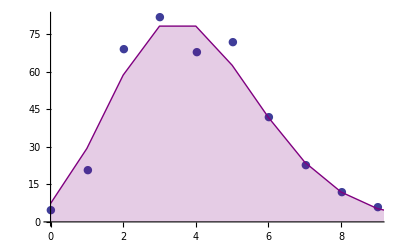

0.371567

```mathematica
distroPlot =ListPlot[distro0, PlotMarkers->{Automatic,Medium}];
simple = simpleData[distro0];
mean = Mean[simple];
ndPlot =DiscretePlot[Length[simple]*PDF[PoissonDistribution[mean], x],{x,0,Length[distro0]}, PlotStyle->Purple, Joined->True];
Show[distroPlot, ndPlot]
PearsonChiSquareTest[simple, PoissonDistribution[mean]]
```